```mathematica
dx1=0;
dx2=0;
dx3=0;

ds1=0;
ds2=0;
ds3=0;



X[1]=-1/2;
X[2]=1;
X[3]=-1/2;
X[4]=1/2;
X[5]=-1;
X[6]=1/2;

Y[1]=Sqrt[3]/2;
Y[2]=0;
Y[3]=-Sqrt[3]/2;
Y[4]=Sqrt[3]/2;
Y[5]=0;
Y[6]=-Sqrt[3]/2;



Z[1]=0;
Z[2]=0;
Z[3]=0;
Z[4]=0;
Z[5]=0;
Z[6]=0;

For[i=1,i≤6,i++,S[i]=Sqrt[X[i]^2+Y[i]^2+Z[i]^2]];
For[i=1,i≤6,i++,VN[i]={X[i],Y[i],Z[i]}/S[i]];
For[i=1,i≤6,i++,VN1[i]={-Y[i],X[i],0}/Sqrt[X[i]^2+Y[i]^2]];
For[i=1,i≤6,i++,VN2[i]=Cross[VN[i],VN1[i]]];
Clear[S1,S2,kx,ky]
NSS[1]=-S[1] VN[1];
NSS[2]=-S[2]VN[2];
NSS[3]=-2S[3]VN[3];
NSS[4]=-2S[4]VN[4];
NSS[5]=-S[5]VN[5];
NSS[6]=-S[6]VN[6];

NDS[1]=S1[2]VN1[2]+S1[3]VN1[3]+S2[2]VN2[2]+S2[3]VN2[3];
NDS[2]=S1[1]VN1[1]+S1[3]VN1[3]+S2[3]VN2[3];
NDS[3]=S1[1]VN1[1]+S1[2]VN1[2]+S1[4]VN1[4]+S2[2]VN2[2];
NDS[4]=S1[3]VN1[3]+S1[5]VN1[5]+S1[6]VN1[6]+S2[3]VN2[3]+S2[5]VN2[5]+S2[6]VN2[6];
NDS[5]=S1[4]VN1[4]+S1[6]VN1[6]+S2[6]VN2[6];
NDS[6]=S1[4]VN1[4]+S1[5]VN1[5]+S2[5]VN2[5];

DTS1[1]=VN1[1].Cross[S[1]VN[1],(S[1]Cross[VN[1],NDS[1]]+S1[1]Cross[VN1[1],NSS[1]])];
DTS1[4]=VN1[4].Cross[S[4]VN[4],(S[4]Cross[VN[4],NDS[4]]+S1[4]Cross[VN1[4],NSS[4]])];
DTS1[2]=VN1[2].Cross[S[2]VN[2],(S[2]Cross[VN[2],NDS[2]]+S2[2]Cross[VN2[2],NSS[2]]+S1[2]Cross[VN1[2],NSS[2]])];
DTS1[3]=VN1[3].Cross[S[3]VN[3],(S[3]Cross[VN[3],NDS[3]]+S2[3]Cross[VN2[3],NSS[3]]+S1[3]Cross[VN1[3],NSS[3]])];
DTS1[5]=VN1[5].Cross[S[5]VN[5],(S[5]Cross[VN[5],NDS[5]]+S2[5]Cross[VN2[5],NSS[5]]+S1[5]Cross[VN1[5],NSS[5]])];
DTS1[6]=VN1[6].Cross[S[6]VN[6],(S[6]Cross[VN[6],NDS[6]]+S2[6]Cross[VN2[6],NSS[6]]+S1[6]Cross[VN1[6],NSS[6]])];

DTS2[2]=VN2[2].Cross[S[2]VN[2],(S[2]Cross[VN[2],NDS[2]]+S2[2]Cross[VN2[2],NSS[2]]+S1[2]Cross[VN1[2],NSS[2]])];
DTS2[3]=VN2[3].Cross[S[3]VN[3],(S[3]Cross[VN[3],NDS[3]]+S2[3]Cross[VN2[3],NSS[3]]+S1[3]Cross[VN1[3],NSS[3]])];
DTS2[5]=VN2[5].Cross[S[5]VN[5],(S[5]Cross[VN[5],NDS[5]]+S2[5]Cross[VN2[5],NSS[5]]+S1[5]Cross[VN1[5],NSS[5]])];
DTS2[6]=VN2[6].Cross[S[6]VN[6],(S[6]Cross[VN[6],NDS[6]]+S2[6]Cross[VN2[6],NSS[6]]+S1[6]Cross[VN1[6],NSS[6]])];



DNMM1D=CoefficientArrays[Flatten[{Table[DTS1[i],{i,1,6}],Table[DTS2[i],{i,{2,3,5,6}}]}]==0,Flatten[{Table[S1[i],{i,1,6}],Table[S2[i],{i,{2,3,5,6}}]}]][[2]];
Clear[HH1D]
MatrixForm[DNMM1D]
```

```mathematica
HH1D=-({{-1, 1/2, 1/2, 0, 0, 0, 0, 0, 0, 0}, {1/2, -1, 1/2, 0, 0, 0, 0, 0, 0, 0}, {1/2, 1/2, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -2, 1/2, 1/2, 0, 0, 0, 0}, {0, 0, 0, 1/2, -1, 1/2, 0, 0, 0, 0}, {0, 0, 0, 1/2, 1/2, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, -1, 0, 0}, {0, 0, 0, 0, 0, 0, -1, -2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, -1}, {0, 0, 0, 0, 0, 0, 0, 0, -1, -1}})
```

SparseArray[<28>,{10,10}]

```mathematica
EE1D[kx_]:=Sort[Sqrt[Re[Eigenvalues[HH1D[kx]]]]];
```

```mathematica
Eigensystem[HH1D]
```

{{1/4 (7+√33),1/2 (3+√5),2,3/2,3/2,3/2,1/2 (3-√5),1/4 (7-√33),0,0},{{-1,-1,1/2 (5+√33),1/2 (-5-√33),1,1,0,0,0,0},{0,0,0,0,0,0,1/2 (-1+√5),1,0,0},{0,0,0,0,0,0,0,0,1,1},{1,0,-1,-1,0,1,0,0,0,0},{1,0,-1,-1,1,0,0,0,0,0},{-1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1/2 (-1-√5),1,0,0},{-1,-1,1/2 (5-√33),1/2 (-5+√33),1,1,0,0,0,0},{0,0,0,0,0,0,0,0,-1,1},{1,1,1,1,1,1,0,0,0,0}}}

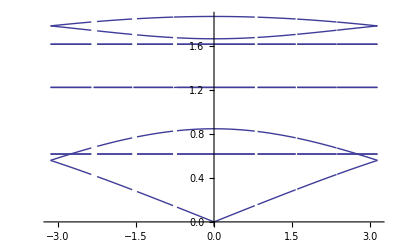

```mathematica
Plot[EE1D[kx],{kx,-Pi,Pi}]
```